```mathematica
w2=2/(0.5s+1);w3=16/(s+4);w4=4;
(544+24 s+4 s^2)/(72+6s+s^2)
```

(544+24 s+4 s^2)/(72+6 s+s^2)

```mathematica
kk=.;b=.;
```

```mathematica
kk=1;b=1;
```

```mathematica
q[a_]:=kk-(2kk)/Pi(ArcSin[b/a]+b/a*Sqrt[1-(b/a)^2])

Plot[q[a], {a, 0, 20},PlotRange->Full]
```

-Graphics-

```mathematica
Clear[q]
d[s_]:=(s^2+6s+72)+k*q[a]*(544+24 s+4 s^2)
d[I*w]//FullSimplify
```

72-w (-6 ⅈ+w)-4 k (-136+w (-6 ⅈ+w)) q[a]

```mathematica
re=72-w^2-4 k q [a](-136+w^2);
im=(6 +24k q [a])w ;
```

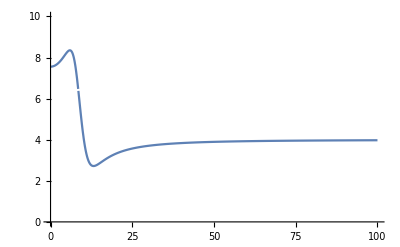

```mathematica
Plot[Abs[(544+24 I*w+4 (I*w)^2)/(72+6I*w+(I*w)^2)], {w, 0, 100}, PlotRange->{0,10}]
```

```mathematica
im//FullSimplify
```

w (6+(48 k kk (-b √(1-b^2/a^2)+a ArcCos[b/a]))/(a π))

```mathematica
w^2==
```

{{w→-(√(-72+(1088 b √(1-b^2/a^2) k kk)/(a π)-(1088 k kk ArcCos[b/a])/π))/(√(-1+(8 b √(1-b^2/a^2) k kk)/(a π)-(8 k kk ArcCos[b/a])/π))},{w→(√(-72+(1088 b √(1-b^2/a^2) k kk)/(a π)-(1088 k kk ArcCos[b/a])/π))/(√(-1+(8 b √(1-b^2/a^2) k kk)/(a π)-(8 k kk ArcCos[b/a])/π))}}

```mathematica
im
```